## Integración Numérica

```mathematica
metodoTrapecio[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n-1,i++,
sum =sum+f[a+i*h];];
Return[h/2(f[a]+f[b])+h*sum];
];
```

```mathematica
f[x_]:=Exp[-x^2]
```

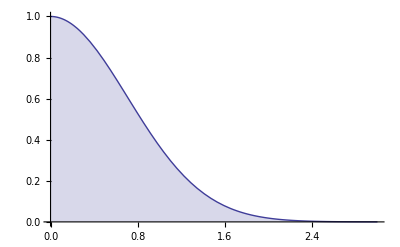

```mathematica
Plot[f[x],{x,0,3},Filling->Bottom]
```

```mathematica
NIntegrate[f[x],{x,0,3}]
```

0.886207

```mathematica
metodoTrapecio[0,3,5]
```

0.886188

```mathematica
TableForm[
Table[{i,NIntegrate[f[x],{x,0,3}],
NumberForm[metodoTrapecio[0,3,i],{10,10}],
Abs[(NIntegrate[f[x],{x,0,3}]-metodoTrapecio[0,3,i])/NIntegrate[f[x],{x,0,3}]*100]},{i,1,30}]]
```

1 | 0.886207 | 1.5001851150 | 69.2815
2 | 0.886207 | 0.9081913942 | 2.48069
3 | 0.886207 | 0.8862567850 | 0.00557846
4 | 0.886207 | 0.8861801022 | 0.00307445
5 | 0.886207 | 0.8861884778 | 0.00212935
6 | 0.886207 | 0.8861936234 | 0.00154872
7 | 0.886207 | 0.8861969638 | 0.00117179
8 | 0.886207 | 0.8861992394 | 0.000915004
9 | 0.886207 | 0.8862008523 | 0.000733005
10 | 0.886207 | 0.8862020336 | 0.000599704
11 | 0.886207 | 0.8862029230 | 0.000499343
12 | 0.886207 | 0.8862036085 | 0.000421998
13 | 0.886207 | 0.8862041474 | 0.000361189
14 | 0.886207 | 0.8862045784 | 0.000312548
15 | 0.886207 | 0.8862049284 | 0.000273053
16 | 0.886207 | 0.8862052164 | 0.000240559
17 | 0.886207 | 0.8862054561 | 0.000213511
18 | 0.886207 | 0.8862056577 | 0.000190762
19 | 0.886207 | 0.8862058288 | 0.000171451
20 | 0.886207 | 0.8862059753 | 0.000154921
21 | 0.886207 | 0.8862061017 | 0.000140663
22 | 0.886207 | 0.8862062114 | 0.000128281
23 | 0.886207 | 0.8862063073 | 0.000117461
24 | 0.886207 | 0.8862063916 | 0.000107951
25 | 0.886207 | 0.8862064661 | 0.0000995477
26 | 0.886207 | 0.8862065322 | 0.0000920871
27 | 0.886207 | 0.8862065911 | 0.0000854332
28 | 0.886207 | 0.8862066440 | 0.000079474
29 | 0.886207 | 0.8862066914 | 0.0000741162
30 | 0.886207 | 0.8862067343 | 0.0000692817

## Sumas de Riemann

```mathematica
(** Suma Inferior **)
```

```mathematica
sumaInferior[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=0,i≤ n-1,i++,
sum =sum+h*f[a+i*h];];
Return[sum];
];
```

```mathematica
sumaInferior[0,3,50]
```

0.916203

```mathematica
TableForm[
Table[{i,NIntegrate[f[x],{x,0,3}],
NumberForm[sumaInferior[0,3,i],{10,10}],
Abs[(NIntegrate[f[x],{x,0,3}]-sumaInferior[0,3,i])/NIntegrate[f[x],{x,0,3}]*100]},{i,1,30}]]
```

1 | 0.886207 | 3.0000000000 | 238.521
2 | 0.886207 | 1.6580988370 | 87.1006
3 | 0.886207 | 1.3861950800 | 56.4188
4 | 0.886207 | 1.2611338240 | 42.3069
5 | 0.886207 | 1.1861514550 | 33.8458
6 | 0.886207 | 1.1361627710 | 28.2051
7 | 0.886207 | 1.1004562330 | 24.1759
8 | 0.886207 | 1.0736761000 | 21.1541
9 | 0.886207 | 1.0528469510 | 18.8037
10 | 0.886207 | 1.0361835220 | 16.9234
11 | 0.886207 | 1.0225497310 | 15.3849
12 | 0.886207 | 1.0111881820 | 14.1029
13 | 0.886207 | 1.0015745230 | 13.0181
14 | 0.886207 | 0.9933342131 | 12.0882
15 | 0.886207 | 0.9861925875 | 11.2824
16 | 0.886207 | 0.9799436467 | 10.5772
17 | 0.886207 | 0.9744298611 | 9.95506
18 | 0.886207 | 0.9695287069 | 9.40202
19 | 0.886207 | 0.9651434544 | 8.90718
20 | 0.886207 | 0.9611967196 | 8.46183
21 | 0.886207 | 0.9576258581 | 8.05889
22 | 0.886207 | 0.9543796153 | 7.69259
23 | 0.886207 | 0.9514156502 | 7.35813
24 | 0.886207 | 0.9486986785 | 7.05155
25 | 0.886207 | 0.9461990615 | 6.76949
26 | 0.886207 | 0.9438917201 | 6.50913
27 | 0.886207 | 0.9417552906 | 6.26805
28 | 0.886207 | 0.9397714613 | 6.0442
29 | 0.886207 | 0.9379244461 | 5.83578
30 | 0.886207 | 0.9362005638 | 5.64125

```mathematica
sumaSuperior[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/n;
sum = 0;
For[i=1,i≤ n,i++,
sum =sum+h*f[a+i*h];];
Return[sum];
];
```

```mathematica
sumaSuperior[0,3,5]
```

0.586226

```mathematica
TableForm[
Table[{i,NIntegrate[f[x],{x,0,3}],
NumberForm[sumaSuperior[0,3,i],{10,10}],
Abs[(NIntegrate[f[x],{x,0,3}]-sumaSuperior[0,3,i])/NIntegrate[f[x],{x,0,3}]*100]},{i,1,30}]]
```

1 | 0.886207 | 0.0003702294 | 99.9582
2 | 0.886207 | 0.1582839515 | 82.1392
3 | 0.886207 | 0.3863184899 | 56.4077
4 | 0.886207 | 0.5112263809 | 42.313
5 | 0.886207 | 0.5862255008 | 33.8501
6 | 0.886207 | 0.6362244758 | 28.2082
7 | 0.886207 | 0.6719376944 | 24.1783
8 | 0.886207 | 0.6987223788 | 21.1559
9 | 0.886207 | 0.7195547539 | 18.8051
10 | 0.886207 | 0.7362205451 | 16.9246
11 | 0.886207 | 0.7498561153 | 15.3859
12 | 0.886207 | 0.7612190347 | 14.1037
13 | 0.886207 | 0.7708337716 | 13.0188
14 | 0.886207 | 0.7790749438 | 12.0889
15 | 0.886207 | 0.7862172694 | 11.2829
16 | 0.886207 | 0.7924667861 | 10.5777
17 | 0.886207 | 0.7979810511 | 9.95549
18 | 0.886207 | 0.8028826085 | 9.4024
19 | 0.886207 | 0.8072682033 | 8.90753
20 | 0.886207 | 0.8112152311 | 8.46214
21 | 0.886207 | 0.8147863453 | 8.05918
22 | 0.886207 | 0.8180328075 | 7.69284
23 | 0.886207 | 0.8209969645 | 7.35837
24 | 0.886207 | 0.8237141047 | 7.05176
25 | 0.886207 | 0.8262138706 | 6.76969
26 | 0.886207 | 0.8285213443 | 6.50931
27 | 0.886207 | 0.8306578917 | 6.26822
28 | 0.886207 | 0.8326418266 | 6.04436
29 | 0.886207 | 0.8344889368 | 5.83593
30 | 0.886207 | 0.8362129048 | 5.64139

```mathematica
TableForm[
Table[{i,NIntegrate[f[x],{x,0,3}],
NumberForm[sumaInferior[0,3,i],{10,10}],NumberForm[sumaSuperior[0,3,i],{10,10}],
Abs[(NIntegrate[f[x],{x,0,3}]-sumaInferior[0,3,i])/NIntegrate[f[x],{x,0,3}]*100], Abs[(NIntegrate[f[x],{x,0,3}]-sumaSuperior[0,3,i])/NIntegrate[f[x],{x,0,3}]*100]},{i,1,30}] ,TableHeadings->{None,{"Índice","Valor Real", "Suma Inferior", "Suma Superior","E.V.R.P. Suma Inferior","E.V.R.P. Suma Superior"}}]
```

Índice | Valor Real | Suma Inferior | Suma Superior | E.V.R.P. Suma Inferior | E.V.R.P. Suma Superior
1 | 0.886207 | 3.0000000000 | 0.0003702294 | 238.521 | 99.9582
2 | 0.886207 | 1.6580988370 | 0.1582839515 | 87.1006 | 82.1392
3 | 0.886207 | 1.3861950800 | 0.3863184899 | 56.4188 | 56.4077
4 | 0.886207 | 1.2611338240 | 0.5112263809 | 42.3069 | 42.313
5 | 0.886207 | 1.1861514550 | 0.5862255008 | 33.8458 | 33.8501
6 | 0.886207 | 1.1361627710 | 0.6362244758 | 28.2051 | 28.2082
7 | 0.886207 | 1.1004562330 | 0.6719376944 | 24.1759 | 24.1783
8 | 0.886207 | 1.0736761000 | 0.6987223788 | 21.1541 | 21.1559
9 | 0.886207 | 1.0528469510 | 0.7195547539 | 18.8037 | 18.8051
10 | 0.886207 | 1.0361835220 | 0.7362205451 | 16.9234 | 16.9246
11 | 0.886207 | 1.0225497310 | 0.7498561153 | 15.3849 | 15.3859
12 | 0.886207 | 1.0111881820 | 0.7612190347 | 14.1029 | 14.1037
13 | 0.886207 | 1.0015745230 | 0.7708337716 | 13.0181 | 13.0188
14 | 0.886207 | 0.9933342131 | 0.7790749438 | 12.0882 | 12.0889
15 | 0.886207 | 0.9861925875 | 0.7862172694 | 11.2824 | 11.2829
16 | 0.886207 | 0.9799436467 | 0.7924667861 | 10.5772 | 10.5777
17 | 0.886207 | 0.9744298611 | 0.7979810511 | 9.95506 | 9.95549
18 | 0.886207 | 0.9695287069 | 0.8028826085 | 9.40202 | 9.4024
19 | 0.886207 | 0.9651434544 | 0.8072682033 | 8.90718 | 8.90753
20 | 0.886207 | 0.9611967196 | 0.8112152311 | 8.46183 | 8.46214
21 | 0.886207 | 0.9576258581 | 0.8147863453 | 8.05889 | 8.05918
22 | 0.886207 | 0.9543796153 | 0.8180328075 | 7.69259 | 7.69284
23 | 0.886207 | 0.9514156502 | 0.8209969645 | 7.35813 | 7.35837
24 | 0.886207 | 0.9486986785 | 0.8237141047 | 7.05155 | 7.05176
25 | 0.886207 | 0.9461990615 | 0.8262138706 | 6.76949 | 6.76969
26 | 0.886207 | 0.9438917201 | 0.8285213443 | 6.50913 | 6.50931
27 | 0.886207 | 0.9417552906 | 0.8306578917 | 6.26805 | 6.26822
28 | 0.886207 | 0.9397714613 | 0.8326418266 | 6.0442 | 6.04436
29 | 0.886207 | 0.9379244461 | 0.8344889368 | 5.83578 | 5.83593
30 | 0.886207 | 0.9362005638 | 0.8362129048 | 5.64125 | 5.64139

## Método de Simpson

```mathematica
simpson[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/(2*n);
sumPar = 0;
For[i=1,i≤ n-1,i++,
sumPar =sumPar+f[a+i*h*2];];
sumImpar = 0;
For[i=1,i≤ n,i++,
sumImpar =sumImpar+f[a+h*(2*i-1)];];
Return[h/3(f[a]+f[b]+2*sumPar+4*sumImpar)];
];
```

```mathematica
simpson[0,3,5]
```

0.886207

```mathematica
NIntegrate[f[x],{x,0,3}]
```

0.886207

```mathematica
TableForm[
Table[{i,NIntegrate[f[x],{x,0,3}],
NumberForm[metodoTrapecio[0,3,i],{10,10}],
NumberForm[simpson[0,3,i],{10,10}],
Abs[(NIntegrate[f[x],{x,0,3}]-metodoTrapecio[0,3,i])/NIntegrate[f[x],{x,0,3}]*100],Abs[(NIntegrate[f[x],{x,0,3}]-simpson[0,3,i])/NIntegrate[f[x],{x,0,3}]*100]},{i,1,30}],TableHeadings->{None,{"Índice","Valor Real", "Método de Trapecio", "Método de Simpson","E.V.R.P. Método de Trapecio","E.V.R.P. Método de Simpson"}}]
```

Índice | Valor Real | Método de Trapecio | Método de Simpson | E.V.R.P. Método de Trapecio | E.V.R.P. Método de Simpson
1 | 0.886207 | 1.5001851150 | 0.7108601540 | 69.2815 | 19.7862
2 | 0.886207 | 0.9081913942 | 0.8788430049 | 2.48069 | 0.830996
3 | 0.886207 | 0.8862567850 | 0.8861725695 | 0.00557846 | 0.00392445
4 | 0.886207 | 0.8861801022 | 0.8862056185 | 0.00307445 | 0.000195187
5 | 0.886207 | 0.8861884778 | 0.8862065522 | 0.00212935 | 0.0000898225
6 | 0.886207 | 0.8861936234 | 0.8862069369 | 0.00154872 | 0.0000464234
7 | 0.886207 | 0.8861969638 | 0.8862071167 | 0.00117179 | 0.0000261342
8 | 0.886207 | 0.8861992394 | 0.8862072087 | 0.000915004 | 0.000015744
9 | 0.886207 | 0.8862008523 | 0.8862072595 | 0.000733005 | 0.0000100149
10 | 0.886207 | 0.8862020336 | 0.8862072892 | 0.000599704 | 6.6594×10^-6
11 | 0.886207 | 0.8862029230 | 0.8862073075 | 0.000499343 | 4.59376×10^-6
12 | 0.886207 | 0.8862036085 | 0.8862073193 | 0.000421998 | 3.26802×10^-6
13 | 0.886207 | 0.8862041474 | 0.8862073271 | 0.000361189 | 2.38661×10^-6
14 | 0.886207 | 0.8862045784 | 0.8862073325 | 0.000312548 | 1.78263×10^-6
15 | 0.886207 | 0.8862049284 | 0.8862073362 | 0.000273053 | 1.3578×10^-6
16 | 0.886207 | 0.8862052164 | 0.8862073389 | 0.000240559 | 1.05209×10^-6
17 | 0.886207 | 0.8862054561 | 0.8862073409 | 0.000213511 | 8.27635×10^-7
18 | 0.886207 | 0.8862056577 | 0.8862073424 | 0.000190762 | 6.59885×10^-7
19 | 0.886207 | 0.8862058288 | 0.8862073435 | 0.000171451 | 5.32508×10^-7
20 | 0.886207 | 0.8862059753 | 0.8862073444 | 0.000154921 | 4.34398×10^-7
21 | 0.886207 | 0.8862061017 | 0.8862073451 | 0.000140663 | 3.57853×10^-7
22 | 0.886207 | 0.8862062114 | 0.8862073456 | 0.000128281 | 2.97433×10^-7
23 | 0.886207 | 0.8862063073 | 0.8862073461 | 0.000117461 | 2.49231×10^-7
24 | 0.886207 | 0.8862063916 | 0.8862073464 | 0.000107951 | 2.10402×10^-7
25 | 0.886207 | 0.8862064661 | 0.8862073467 | 0.0000995477 | 1.78843×10^-7
26 | 0.886207 | 0.8862065322 | 0.8862073469 | 0.0000920871 | 1.52981×10^-7
27 | 0.886207 | 0.8862065911 | 0.8862073471 | 0.0000854332 | 1.31626×10^-7
28 | 0.886207 | 0.8862066440 | 0.8862073473 | 0.000079474 | 1.13868×10^-7
29 | 0.886207 | 0.8862066914 | 0.8862073474 | 0.0000741162 | 9.90044×10^-8
30 | 0.886207 | 0.8862067343 | 0.8862073475 | 0.0000692817 | 8.64877×10^-8